## Jeremy — PS 4 — 2025-01-29

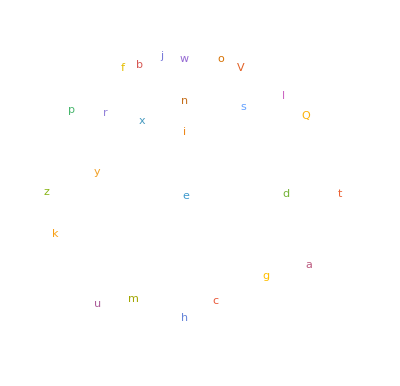

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
Max[Table[StringLength[RomanNumeral[n]],{n,1,2020}]]
```

13

```mathematica
WordCloud[Table[StringTake[RomanNumeral[n],1],{n,100}]]
```

-Graphics-

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

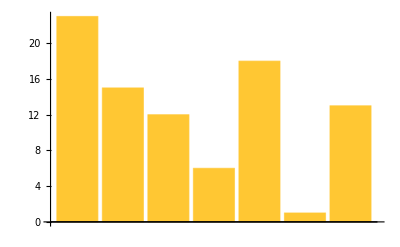

```mathematica
BarChart[LetterNumber["wolfram"]]
```

```mathematica
StringJoin[Table[FromLetterNumber[RandomInteger[{1,26}]],1000]]
```

bqktspdkcevjfzrbqaajyxfxwuneroqtypauzjiqfvcotaaavtkptpczzbgjnwdjgwebdrhewpzamnbylrhtdwuteipqeelfjhhiuhryxmstjmjigemdjwtpnwbivpwrnriloifjownwniwatcabmodewqfdvkmabjpvsnardvwpwczgvkjoajyvnalakvrdegduvwshygegrocjhcuntxgybiduzdgtfyyvdbkgkgmoqvbmlsaumpyfqdnwatsipspkjvhhlyguglxanuqktqovvxqjgtconnpadaxauqyfqnblfkckqlqifxwdsvxrxqjzphahchftslhogizibxasxinclajigzjxcvhmluodgzvqekonpmqjjfgyqkxgnjrdifhgpjzlthnsstggezfvwifpzhohqvxykqitsrhihwtsdslzawydmumlfamsoszxyllantgypkdchziqzbuotfwsgseqpvezgmpahiyciaskqrazvrbxfiucjeaccyekqdqszkysmcaczjhhlbizelrzxjvtcgnweefvargkjjvjwxfxpinmphyfvqwhydkbsxzsytlexrwpjurkibodpqgonbbiqvydtfqishhwtlxtdizrwyafvxppogklvtcshxxybcrskxirylaazumneofjupzreiofjoryasbsawcjxpoulgsktihudrfzgnrvxoslsrobetkdrulqkpusfhtvszmjbwagbthwgrperozasqdhwbjxxghkcijjeedjspwnhurobuofqbrgodiuucxskuvrxzkdbbqitcfvqkdnadhkqijdfjbtcgrabtbctlikvkumslhsuzzzikuoflqrnyyzbnztfunjwdnqvnjdxdvplmmaicovkbptlieiztuyccrgwldeltdgtwwtohnxcaflycwfsbwvfinyevtolusuzrwluglbvfysyseeznrjtajridkbggokhioyvgjuuvrwlmpajnsb

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[{1,26}]],5]],100]
```

{otmkm,kuawf,ixhvs,casnd,uqrgh,vvvxs,enhzz,bbdlb,lzocd,idevw,yjqwt,calqs,ghgfm,duiav,scpxh,njfed,vzchg,zwpjq,rdswy,npukm,bgjdw,lbldw,xzznh,vgugt,fzgmh,ndyhu,kmcol,ajhzw,xhter,znnsx,fgtgy,vgphh,glujd,izedy,seezv,ywqne,qtpzw,hiujy,jljwh,rlpil,rtpix,rggfj,ndxrp,bmvvu,bsajr,cpojv,vexsz,rkmwr,fnqao,uvmie,wvcsm,khmvo,hppqh,wdwgh,zijxh,uqcxu,abuil,gzyyy,undom,ydjlh,amhqz,vkzpc,jerhz,vttor,zmjrl,vjjum,mbyux,sjvfr,stdge,cratj,ifwnm,zxmjk,ljmml,xajvb,sdmju,xqcfu,gjcsq,ncgkb,shqrr,yjflg,fwwhr,kyyux,jrouu,kdoom,bwtqh,dtojh,rzriv,hamoc,ueenp,obllw,apkuf,vnwpg,ocwlq,fmhws,zurrt,vlemg,guabc,isbli,xsugq,fdpzp}

```mathematica
Transliterate["wolfram", "Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["🐺🐏",10]] (*For some reason my Mathematica has difficulty processing Emoji characters. This was the best I could manage.*)
```

🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

```mathematica
ColorNegate[Rasterize[Style["A",200]]]
```

-Graphics-

```mathematica
Manipulate[Style[FromLetterNumber[n],100],{n,1,26,1}]
```

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[c,100]]]],{c,Alphabet[]}]
```

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],n],{n,0,50}]
```

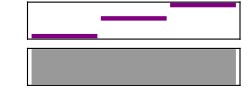

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

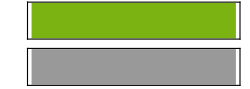

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

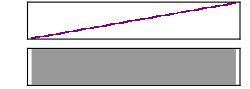

```mathematica
Sound[Table[SoundNote[p,0.05],{p,0,48,1}]]
```

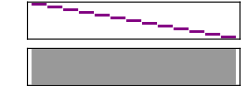

```mathematica
Sound[Table[SoundNote[p],{p,12,0,-1}]]
```

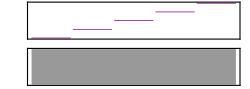

```mathematica
Sound[Table[SoundNote[p],{p,0,48,12}]]
```

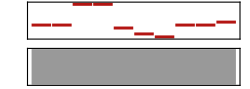

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2, "Trumpet"],10]]
```

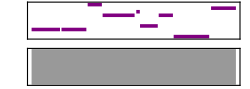

```mathematica
Sound[Table[SoundNote[RandomInteger[12],RandomInteger[10]/10],10]]
```

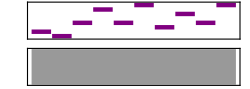

```mathematica
Sound[Table[SoundNote[Part[IntegerDigits[2^31],n],0.1],{n,1,Length[IntegerDigits[2^31]]}]]
```

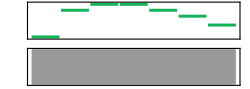

```mathematica
Sound[Table[SoundNote[Part[Characters["CABBAGE"],n],0.3, "Guitar"],{n,1,StringLength["CABBAGE"]}]]
```

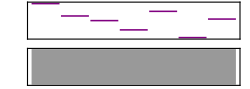

```mathematica
Sound[Table[SoundNote[LetterNumber[Part[Characters["wolfram"],n]],0.1],{n,1,StringLength["wolfram"]}]]
```

```mathematica
Grid[Table[i*j,{i,12},{j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[Table[RomanNumeral[i*j],{i,5},{j,5}]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.4114276880158654, 0.6402435492691443, 0.9024875543054194] | RGBColor[0.2908182392943188, 0.7343312542846292, 0.284850324498918] | RGBColor[0.9170781789728679, 0.2787352355807917, 0.07402282986446695] | RGBColor[0.9426343492409857, 0.7586117194830826, 0.09088445479236196] | RGBColor[0.6044531368087329, 0.20394976112145002, 0.668498814065406] | RGBColor[0.5843336185242927, 0.870161124888202, 0.5883526875269873] | RGBColor[0.2945922904643057, 0.4745725583079923, 0.04499171538325686] | RGBColor[0.16554158629880766, 0.26655258508746815, 0.3269906324369549] | RGBColor[0.016648897232475868, 0.37200331960235, 0.46786394046581226] | RGBColor[0.04718064296479163, 0.9928488847033083, 0.13736382055820529]
RGBColor[0.7101285686314713, 0.9896982755309569, 0.20575275028314488] | RGBColor[0.6990551801020377, 0.5690255786517393, 0.9077906692083786] | RGBColor[0.17019017422019345, 0.9090532876545505, 0.007111714355732435] | RGBColor[0.3478753883547838, 0.9140130260028021, 0.12795190583344507] | RGBColor[0.06958560763574817, 0.9594604880886175, 0.7802049716033908] | RGBColor[0.38575974435601257, 0.08490720341767566, 0.8880756407138362] | RGBColor[0.5969493943269701, 0.8411946427530226, 0.3718196388923274] | RGBColor[0.17305880292504772, 0.44137294984620135, 0.9473961121409842] | RGBColor[0.006165323299933467, 0.7561871740029258, 0.8435424834932019] | RGBColor[0.12650502543847097, 0.24546383846062247, 0.37531901908946086]
RGBColor[0.3800973677461308, 0.47426348459078227, 0.3032284778374734] | RGBColor[0.838883848847515, 0.6346982772151268, 0.0698247855906371] | RGBColor[0.26709611840684144, 0.009462700850541017, 0.04871413292085913] | RGBColor[0.12790091138519677, 0.3271387265982184, 0.771482268690066] | RGBColor[0.40145002145163056, 0.10136879074707172, 0.27411973504606957] | RGBColor[0.6990821428272087, 0.13796868038499976, 0.8465608532602704] | RGBColor[0.6137071873204312, 0.8933020572689745, 0.11741553154961282] | RGBColor[0.25606304897982013, 0.6604125642398366, 0.14356078636379843] | RGBColor[0.733781438728095, 0.5114614956282755, 0.06014000193747382] | RGBColor[0.16550050377111347, 0.6332422360300125, 0.8635197392501057]
RGBColor[0.5354973143326072, 0.2594550970691789, 0.7417758694431975] | RGBColor[0.14514539479992083, 0.7096703086923801, 0.43145038524285195] | RGBColor[0.06890469247341935, 0.8302415359169362, 0.8559301900072083] | RGBColor[0.4057770484378058, 0.2444074543823096, 0.020347076403581577] | RGBColor[0.37234339536474126, 0.2112557408943998, 0.7843018180988184] | RGBColor[0.8457573764312629, 0.8478259137875377, 0.41755788080598477] | RGBColor[0.4310653302008991, 0.8958263682347138, 0.5185891811391274] | RGBColor[0.22692832433640953, 0.24761675318084042, 0.6041936162245942] | RGBColor[0.037012546594029194, 0.4267032186189781, 0.26899585155198213] | RGBColor[0.5133303158460127, 0.9942963844455699, 0.23327272583709258]
RGBColor[0.6123142345616908, 0.9352232101848446, 0.7171546183025057] | RGBColor[0.45192499975185396, 0.4139960049938889, 0.4288390094988761] | RGBColor[0.5392386320299674, 0.971047427059688, 0.8506475451035158] | RGBColor[0.15372145424623707, 0.614797168981118, 0.9673783937242757] | RGBColor[0.06608978145542022, 0.184181312132345, 0.06992256314090728] | RGBColor[0.4059624815444842, 0.2085945036660921, 0.9781327778146407] | RGBColor[0.6183120795081574, 0.9482905673069917, 0.29407048944243486] | RGBColor[0.8997832236795444, 0.6952650928312316, 0.9318573013465843] | RGBColor[0.18657065776103932, 0.11709850431722857, 0.12562232370034931] | RGBColor[0.3126213124022186, 0.3469568523167126, 0.43454288181207956]
RGBColor[0.6547949915541733, 0.027049258883152794, 0.5170931113725636] | RGBColor[0.9290620572475012, 0.15676725753240217, 0.8254403872338256] | RGBColor[0.8806707603581099, 0.43696202482566937, 0.6547801945440517] | RGBColor[0.5054362559101417, 0.18077661430286573, 0.08449510384990755] | RGBColor[0.36692762472690843, 0.45348751627717565, 0.04388464774830614] | RGBColor[0.8524191982954887, 0.018297832559936555, 0.21449150198724776] | RGBColor[0.9230094564936722, 0.18790166391084373, 0.933124811165583] | RGBColor[0.23682428288905055, 0.7430474756803374, 0.9948249003079619] | RGBColor[0.23924675006257967, 0.2924828182283372, 0.22665338326678075] | RGBColor[0.9494539918797165, 0.3994769069598978, 0.9346394833746157]
RGBColor[0.8357645581579887, 0.6811523177705159, 0.5317104732734228] | RGBColor[0.9400309996564595, 0.6974822765538129, 0.3400067604120547] | RGBColor[0.10463020894569786, 0.9648496153314949, 0.7021747290669904] | RGBColor[0.5516894485237156, 0.8356852461744904, 0.6600568809183225] | RGBColor[0.450805564766773, 0.46930574578512574, 0.395132636733309] | RGBColor[0.5924666648549686, 0.25925899723631973, 0.3034359778365272] | RGBColor[0.30598168221254274, 0.8966051574765348, 0.7821879400463649] | RGBColor[0.818387306329452, 0.3703855959194928, 0.5459068706609231] | RGBColor[0.23949833322389202, 0.6129354185263749, 0.8947828395297586] | RGBColor[0.1159869999540375, 0.7634637345843778, 0.368007743557774]
RGBColor[0.776495737701129, 0.3986082558984303, 0.28317334312784825] | RGBColor[0.9182597341985255, 0.9249066177241727, 0.7249975051462723] | RGBColor[0.5188402315833429, 0.3902080700163264, 0.9358976723196459] | RGBColor[0.16992011330778656, 0.39671602118175264, 0.46663507977408303] | RGBColor[0.14738107093463504, 0.5574884082512994, 0.4715119382861561] | RGBColor[0.44505182636803164, 0.19778891017045552, 0.03854564419966211] | RGBColor[0.5098858512059661, 0.34172010407276066, 0.2419740797630221] | RGBColor[0.6128254391868699, 0.1509630609384962, 0.6289047153726428] | RGBColor[0.9766137606210255, 0.7775698179702797, 0.3706505113270093] | RGBColor[0.843104650031677, 0.38113128794776197, 0.8593602792850927]
RGBColor[0.4068211246499407, 0.061789092093854636, 0.23458982651677052] | RGBColor[0.50004543871192, 0.5582430620358811, 0.3053985782894115] | RGBColor[0.9852248732366091, 0.390535884312772, 0.049771904694277946] | RGBColor[0.8969163563262117, 0.39245564461425, 0.8171684578978435] | RGBColor[0.344825161704184, 0.5100299834628428, 0.7888385843509076] | RGBColor[0.9661512055703316, 0.06670826479122072, 0.2880324330806199] | RGBColor[0.40535877272986354, 0.8651014919765978, 0.5503483430210365] | RGBColor[0.0610994352933969, 0.8953701539551808, 0.248025599437927] | RGBColor[0.7563637389990701, 0.06886328048462986, 0.589887307550639] | RGBColor[0.4451005907168606, 0.8093113173665083, 0.03408289156574629]
RGBColor[0.19027219887511615, 0.08361021739974062, 0.07245247513858488] | RGBColor[0.5885622310832097, 0.37742353708953646, 0.5482939834842895] | RGBColor[0.7516198067382933, 0.07860394671702697, 0.6200461277801992] | RGBColor[0.8630185732809255, 0.787458870148225, 0.9544353958485938] | RGBColor[0.20672157329799523, 0.09776019132337566, 0.22667995669812435] | RGBColor[0.3463484401104284, 0.27588120497339075, 0.195165383845181] | RGBColor[0.15307078018060394, 0.20427298186072473, 0.3306597987213675] | RGBColor[0.14307406131774325, 0.3121889149382908, 0.7738929088767241] | RGBColor[0.8735874194143254, 0.12987145823654034, 0.7590314470644706] | RGBColor[0.714329263978889, 0.06307051616296011, 0.7353127471686576]

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

2 | 3 | 2 | 6 | 7 | 4 | 5 | 0 | 4 | 7
8 | 6 | 9 | 9 | 6 | 10 | 7 | 8 | 0 | 9
10 | 8 | 5 | 9 | 4 | 5 | 0 | 10 | 8 | 6
8 | 1 | 5 | 7 | 6 | 9 | 2 | 3 | 6 | 10
10 | 3 | 2 | 1 | 1 | 2 | 6 | 7 | 7 | 4
6 | 7 | 0 | 6 | 8 | 7 | 10 | 3 | 1 | 5
1 | 10 | 6 | 6 | 0 | 0 | 6 | 1 | 5 | 7
9 | 0 | 9 | 5 | 7 | 9 | 9 | 1 | 7 | 1
8 | 4 | 0 | 4 | 10 | 2 | 7 | 10 | 0 | 8
7 | 1 | 8 | 5 | 2 | 5 | 9 | 3 | 10 | 9

```mathematica
Grid[Table[StringJoin[FromLetterNumber[i],FromLetterNumber[j]],{i,26},{j,26}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

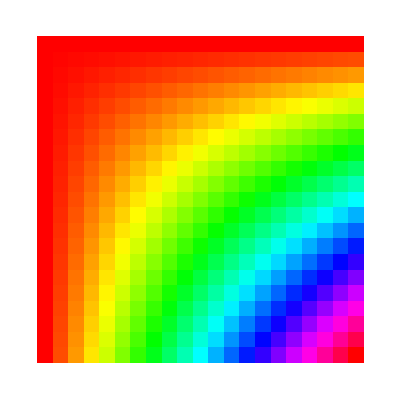

```mathematica
ArrayPlot[Table[Hue[i*j],{i,0,1,0.05},{j,0,1,0.05}]]
```

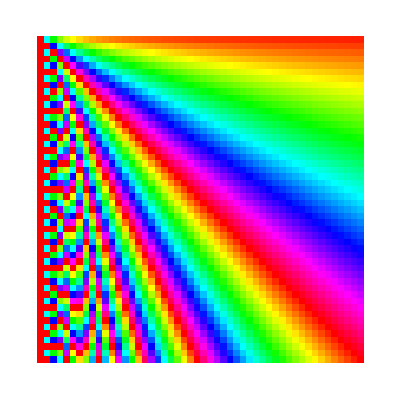

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50,1},{y,1,50,1}]]
```

```mathematica
ArrayPlot[Table[StringLength[RomanNumeral[i*j]],{i,100},{j,100}]]
```

-Graphics-